# ■Tesis final

## Inicialización

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{NotebookDirectory[],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

## Cargar base de datos

```mathematica
path = FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}];
database = Import[path];
database[[All,"Name"]] = {"DJIA","DAX","IPC","Nikkei 225"};
```

## Fechas percentuales

```mathematica
DaysInYear[year_] := First[DateDifference[{year, 1, 1}, {year, 12, 31}]] + 1;

YearPercentual[date_] := N[QuantityMagnitude[DateDifference[DateObject[{date["Year"], 1, 1}], date]] / DaysInYear[date["Year"]]] + date["Year"];

DateFromYearPercentual[yearPercentual_] := Block[{year, daysEllapsed, date},
	year = IntegerPart[yearPercentual];
	daysEllapsed = IntegerPart[(yearPercentual - year) * DaysInYear[year]];
	date = DatePlus[DateObject[{year, 1, 1}], daysEllapsed];
	Return[date];
];
```

```mathematica
Ventana[market_,dias_]:=MovingAverage[MapAt[YearPercentual, database[[market]]["DatedPrices"], {All,1}],dias];
```

## Volver las fechas percentuales a fechas normales

```mathematica
FechasNormales[market_,dias_]:=Block[{Ventana},
Ventana=MovingAverage[MapAt[YearPercentual, database[[market]]["DatedPrices"], {All,1}],dias];
];
```

## Código para tener MAV que automatice el proceso de fechas percentuales y precios de cualquier mercado

```mathematica
MAV[market_,dias_]:=Block[{ventana,MAVDates,MAVPrices},
ventana = MovingAverage[MapAt[YearPercentual, database[[market]]["DatedPrices"], {All,1}],dias];
MAVDates = Map[DateFromYearPercentual[#]&,ventana[[All,1]]];
MAVPrices = ventana[[All,2]];
Transpose[{MAVDates,MAVPrices}]
];
```

## Retornos de los precios a partir de cualquier MAV sobre cualquier mercado

En la siguiente ventana de inicialización se tiene que se pueden calcular los retornos de los precios para los MAV de cualquier mercado y en cualquier ventana de tiempo

```mathematica
MAVReturns[market_,dias_]:=Block[{ventana,MAVDates,MAVPrices,MAVDatePrice,ReturnLogs,DatesLogReturn},
ventana = MovingAverage[MapAt[YearPercentual, database[[market]]["DatedPrices"], {All,1}],dias];
MAVDates = Map[DateFromYearPercentual[#]&,ventana[[All,1]]];
MAVPrices = ventana[[All,2]];
MAVDatePrice = Transpose[{MAVDates,MAVPrices}];
ReturnLogs = MAVDatePrice[[All,2]]//Returns;
DatesLogReturn = Drop[MAVDatePrice[[All,1]],-1];
Transpose[{DatesLogReturn,ReturnLogs}]
];
```

## Valores estandarizados y discretizados para calcular la entropía

```mathematica
DiscretizeByQuartiles[returns_]:=Block[{cuartailsStandardize,intervStandardize,discreStatesStandarizados,rulesStandarized},
cuartailsStandardize = Quantile[Standardize[returns],{1/4,1/2,3/4}];
intervStandardize = Partition[Join[{-∞},cuartailsStandardize,{∞}],2,1];
discreStatesStandarizados = Range[Length[intervStandardize]];
rulesStandarized = MapThread[x_/;IntervalMemberQ[Interval[#1],x]->#2&,{intervStandardize,discreStatesStandarizados}];

Standardize[returns]/. rulesStandarized
];
```

```mathematica
DiscretizeByQuartiles[
```

## Ahora calcularemos la entropía de los mercados a partir de un MAV dada una ventana temporal

```mathematica
MarketEntropyMAV[market_,dias_]:=Block[{ventana,MAVDates,MAVPrices,DatesLogReturn,MAVDatePrice,discretoConFechas,parts,resultado},
ventana = MovingAverage[MapAt[YearPercentual, database[[market]]["DatedPrices"], {All,1}],dias];
MAVDates = Map[DateFromYearPercentual[#]&,ventana[[All,1]]];
MAVPrices = ventana[[All,2]];
MAVDatePrice = Transpose[{MAVDates,MAVPrices}];
DatesLogReturn = Drop[MAVDatePrice[[All,1]],-1];
discretoConFechas =Transpose[{DatesLogReturn,DiscretizeByQuartiles[MAVReturns[market,dias][[All,2]]]}];
parts = Partition[discretoConFechas,dias,1];
resultado  = Map[
{
Last[#[[All,1]]],
N[Entropy[#[[All,2]]]]
}&,
parts
]
];
PlotMarketEntropyMAV[market_,dias_]:=DateListPlot[MarketEntropyMAV[market,dias],PlotRange->{-1,2},PlotLabel->database[[market]]["Name"]]
```

Cabe desatacar que las graficas para 50 ±10 días de todos los mercados está en MXX_MAV.nb

Comparación con caminante aleatorio
Se procede a comparar el resultado de la entropía con el resultado de una distribución gaussiana.

## Ahora se procede a comparar la ENTROPÍA de los mercados (todos) con el "ruido" del mercado eficiente y su histograma respectivo

```mathematica
MarketCompareEntropyMAV[market_,dias_]:=Block[{MercadoSimuladoMAV,MercadoEficienteConFechasMAV,MercadoPreciosSimulados,MercadoConPrecioSimuladoYFechas,MercadoPorcentuales,MercadoConFechasYPreciosMAV,Particion,SimulatedEntropy,EntropiaEficienteYReal,Histograma},
MercadoSimuladoMAV = RandomVariate[NormalDistribution[],Length[MAVReturns[market,dias][[All,2]]]];
MercadoEficienteConFechasMAV = Transpose[{MAVReturns[market,dias][[All,1]],MercadoSimuladoMAV}];
MercadoPreciosSimulados = Accumulate[MercadoEficienteConFechasMAV[[All,2]]]+Abs[Min[Accumulate[MercadoEficienteConFechasMAV[[All,2]]]]];
MercadoConPrecioSimuladoYFechas =  Transpose[{MAVReturns[market,dias][[All,1]],MercadoPreciosSimulados}];
MercadoPorcentuales = MapAt[YearPercentual,MercadoConPrecioSimuladoYFechas,{All,1}];
MercadoConFechasYPreciosMAV=MapAt[DateFromYearPercentual,MovingAverage[MercadoPorcentuales,dias],{All,1}];
Particion = Partition[Transpose[{MercadoConFechasYPreciosMAV[[All,1]],DiscretizeByQuartiles[MercadoConFechasYPreciosMAV[[All,2]]]}],dias,1];
SimulatedEntropy = Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,Particion];
EntropiaEficienteYReal=DateListPlot[{SimulatedEntropy,MarketEntropyMAV[market,dias]},PlotLabel->database[[market]]["Name"],PlotLegends->{"Mercado eficiente" ,"Datos reales"},PlotRange->{-0.2,1.5}];

Histograma = Histogram[{Map[Entropy,Partition[DiscretizeByQuartiles[MercadoConFechasYPreciosMAV[[All,2]]//Returns],dias,1]],Map[Entropy,Partition[DiscretizeByQuartiles[MAVReturns[market,dias][[All,2]]],dias,1]]},
PlotLabel->database[[market]]["Name"]"Entropías" ,BaseStyle->FontSize->16,ChartStyle->{ColorData[97][1],ColorData[97][2]},ChartLegends->{"Mercado eficiente","Datos reales"},PlotRange->All];
EntropiaEficienteYReal Histograma
];
(*Este es el bueno y arroja la grafica y el histograma*)
```

```mathematica
RandomVariate[NormalDistribution[],Length[MAVReturns[1,1][[All,2]]]]
```

{-0.309339,0.419219,0.895132,1.17433,0.188974,-0.14918,0.898402,-0.159795,6450,-0.792227,-0.587217,-0.382254,-0.536505,-0.457471,0.786229,-0.916423}
 |  |  |  |

Y si se quiere que sean sin los histogramas, entonces se tiene la siguiente celda de inicialización
que describe lo mismo pero sin historamas.

```mathematica
MarketCompareEntropyNoHistMAV[market_,dias_]:=Block[{MercadoSimuladoMAV,MercadoEficienteConFechasMAV,MercadoPreciosSimulados,MercadoConPrecioSimuladoYFechas,MercadoPorcentuales,MercadoConFechasYPreciosMAV,Particion,SimulatedEntropy,EntropiaEficienteYReal,Histograma},
MercadoSimuladoMAV = RandomVariate[NormalDistribution[],Length[MAVReturns[market,dias][[All,2]]]];
MercadoEficienteConFechasMAV = Transpose[{MAVReturns[market,dias][[All,1]],MercadoSimuladoMAV}];
MercadoPreciosSimulados = Accumulate[MercadoEficienteConFechasMAV[[All,2]]]+Abs[Min[Accumulate[MercadoEficienteConFechasMAV[[All,2]]]]];
MercadoConPrecioSimuladoYFechas =  Transpose[{MAVReturns[market,dias][[All,1]],MercadoPreciosSimulados}];
MercadoPorcentuales = MapAt[YearPercentual,MercadoConPrecioSimuladoYFechas,{All,1}];
MercadoConFechasYPreciosMAV=MapAt[DateFromYearPercentual,MovingAverage[MercadoPorcentuales,dias],{All,1}];
Particion = Partition[Transpose[{MercadoConFechasYPreciosMAV[[All,1]],DiscretizeByQuartiles[MercadoConFechasYPreciosMAV[[All,2]]]}],dias,1];
SimulatedEntropy = Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,Particion];
EntropiaEficienteYReal=DateListPlot[{SimulatedEntropy,MarketEntropyMAV[market,dias]},PlotLabel->database[[market]]["Name"],PlotLegends->{"Mercado eficiente" ,"Datos reales"},PlotRange->{-0.2,1.5}];

EntropiaEficienteYReal 
];
(*Este no arroja el histograma cosa que sí hace el EntropyMarket ordinario*)
```

# Minimizar la entropía

### Se tienen dos criterios: 1. A partir de thresholds de la entropia sin MAV 2. Selección de todos los puntos en que la entropía simulada y la real de los mercados tras ser filtrados por un MAV.

## 1. A partir de thresholds de la entropía sin MAV

```mathematica
MarketEntropy[market_,dias_]:=Block[{discretoConFechas,parts,resultado},
discretoConFechas =Transpose[{Drop[database[[market]][["Dates"]],-1],DiscretizeByQuartiles[database[[market]]["Returns"]]}];
parts = Partition[discretoConFechas,dias,1];
resultado  = Map[
{
Last[#[[All,1]]],
N[Entropy[#[[All,2]]]]
}&,
parts
]
];
PlotMarketEntropy[market_,dias_]:=DateListPlot[MarketEntropy[market,dias],PlotRange->{0,1.5},PlotLabel->database[[market]]["Name"]];
```

Ahora si vamos a obtener los puntos de minima entropia  a partir de del criterio 1.

```mathematica
MinEntropyMarket[market_,dias_] := Block[{MercadoSimulado,MercadoEficienteConFechas,Particion,SimulatedEntropy,Techo,MercadoNoGaussiano,BuscarPrecio,Rastreador},
MercadoSimulado = RandomVariate[NormalDistribution[],Length[MarketEntropy[market,dias][[All,2]]]];
MercadoEficienteConFechas = Transpose[{MAVReturns[market,dias][[All,1]],MercadoSimulado}];
Particion = Partition[Transpose[{MercadoEficienteConFechas[[All,1]],DiscretizeByQuartiles[MercadoEficienteConFechas[[All,2]]]}],dias,1];
SimulatedEntropy = Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,Particion];
Techo = N[Quantile[Map[N[Entropy[#[[All,2]]]]&,Particion],0.05]];
MercadoNoGaussiano = Select[MarketEntropy[market,dias],Last[#] < Techo &];
BuscarPrecio[datedPrices_,date_]:=FirstCase[datedPrices,{date,p_}:>p];
(*La siguiente linea de codigo nos da todas las fechas en que se tuvo minima entropia y su precio*)
Rastreador = Map[{#,BuscarPrecio[database[[market]]["DatedPrices"],#]}&,MercadoNoGaussiano[[All,1]]]
];
```

Part::pkspec1: The expression … cannot be used as a part specification.

Part::pspec1: Part specification Dates is not applicable.

Part::pkspec1: The expression … cannot be used as a part specification.

Standardize::vectmat: The first argument is expected to be a vector or matrix.

Join::heads: Heads List and Quantile at positions 1 and 2 are expected to be the same.

Join::heads: Heads Quantile and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

MapThread::mptd: Object Join[{-∞},Quantile[Standardize[«1»],{1/4,1/2,3/4}],Quantile[Standardize[{«1»}⟦<|Name→DJIA,Dates→{«1»},«6»,DatedTrendReturns→{«1»},DatedVelocityTrendReturns→{{Day: ,0.00350946},{Day: ,-0.00135624},«3271»,{Day: ,-0.010412}}|>⟧[Returns]],«1»],{∞}] at position {2, 1} in MapThread[x_/;IntervalMemberQ[Interval[#1],x]→#2&,{Join[{-∞},Quantile[Standardize[«1»],{1/4,1/2,3/4}],Quantile[Standardize[«1»],{1/4,1/2,3/4}],{∞}],{1,2,3,4}}] has only 0 of required 1 dimensions.

Standardize::vectmat: The first argument is expected to be a vector or matrix.

ReplaceAll::reps: {MapThread[x_/;IntervalMemberQ[Interval[Slot[«1»]],x]→#2&,{Join[{-∞},Quantile[Standardize[{«4»}⟦<|Name→DJIA,«8»,DatedVelocityTrendReturns→{{Day: ,0.00350946},{Day: ,-0.00135624},«3271»,{Day: ,-0.010412}}|>⟧[Returns]],{«1»}],«1»,{∞}],«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
MinEntropyMarketReturns[market_,dias_] := Block[{MercadoSimulado,MercadoEficienteConFechas,Particion,SimulatedEntropy,Techo,MercadoNoGaussiano,BuscarPrecio,Rastreador,MinEntropyMarketReturns,Var},
MercadoSimulado = RandomVariate[NormalDistribution[],Length[MarketEntropy[market,dias][[All,2]]]];
MercadoEficienteConFechas = Transpose[{MAVReturns[market,dias][[All,1]],MercadoSimulado}];
Particion = Partition[Transpose[{MercadoEficienteConFechas[[All,1]],DiscretizeByQuartiles[MercadoEficienteConFechas[[All,2]]]}],dias,1];
SimulatedEntropy = Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,Particion];
Techo = N[Quantile[Map[N[Entropy[#[[All,2]]]]&,Particion],0.05]];
MercadoNoGaussiano = Select[MarketEntropy[market,dias],Last[#] < Techo &];
BuscarPrecio[datedPrices_,date_]:=FirstCase[datedPrices,{date,p_}:>p];
(*La siguiente linea de codigo nos da todas las fechas en que se tuvo minima entropia y el retorno de su precio*)

Var=Transpose[{Drop[MercadoNoGaussiano[[All,1]],-1],Map[{#,BuscarPrecio[database[[market]]["DatedPrices"],#]}&,
MercadoNoGaussiano[[All,1]]][[All,2]]//Returns}]
(*Ese [[All,1]] y ese [[All,2]] son porque primero busca las fechas de la columna uno, una vez que encunetra las fechas, a cada elemento encontrado, le calculará su retorno y por ello se necesita invocar a la columna [[All,2]]*)
];
```

### Ahora todo junto SIN MAV

```mathematica
ComparativeMarketEntropyThreshold[market_,dias_]:=Block[{MercadoSimulado,MercadoEficienteConFechas,Particion,SimulatedEntropy,EntropiaEficienteYReal,Techo,Histograma,MercadoNoGaussiano,CantidadNoGaussiana,BuscarPrecio,PlotMinEntropyMarket},
MercadoSimulado = RandomVariate[NormalDistribution[],Length[MarketEntropy[market,dias][[All,2]]]];
MercadoEficienteConFechas = Transpose[{MAVReturns[market,dias][[All,1]],MercadoSimulado}];
Particion = Partition[Transpose[{MercadoEficienteConFechas[[All,1]],DiscretizeByQuartiles[MercadoEficienteConFechas[[All,2]]]}],dias,1];
SimulatedEntropy = Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,Particion];
Techo = N[Quantile[Map[N[Entropy[#[[All,2]]]]&,Particion],0.05]];
EntropiaEficienteYReal = DateListPlot[{SimulatedEntropy,MarketEntropy[market,dias]},GridLines->{{},{Techo}},PlotLabel->database[[market]]["Name"],PlotLegends->{"Mercado eficiente" ,"Datos reales"},PlotRange->{0.9,1.5}];
Histograma = Histogram[{Map[Entropy,Partition[DiscretizeByQuartiles[MercadoSimulado],dias,1]],Map[Entropy,Partition[DiscretizeByQuartiles[database[[market]]["Returns"]],dias,1]]},
PlotLabel->database[[market]]["Name"]"Entropías" ,BaseStyle->FontSize->16,ChartStyle->{ColorData[97][1],ColorData[97][2]},ChartLegends->{"Mercado eficiente","Datos reales"},PlotRange->Full];
MercadoNoGaussiano = Select[MarketEntropy[market,dias],Last[#] < Techo &];
CantidadNoGaussiana = N[Length[MercadoNoGaussiano[[All,2]]]/Length[MarketEntropy[market,dias][[All,2]]]];
(*Ahora con la siguiente linea de codigo se tienen que buscar las fechas en que la entropía fue minima*)
BuscarPrecio[datedPrices_,date_]:=FirstCase[datedPrices,{date,p_}:>p];
PlotMinEntropyMarket = DateListPlot[Map[{#,BuscarPrecio[database[[market]]["DatedPrices"],#]}&,MercadoNoGaussiano[[All,1]]],PlotLabel->database[[market]]["Name"] " precios mínimas entropías",PlotRange->All];
EntropiaEficienteYReal Histograma PlotMinEntropyMarket CantidadNoGaussiana*100  "% de los precios no se comporta Gaussianamente"

];
```

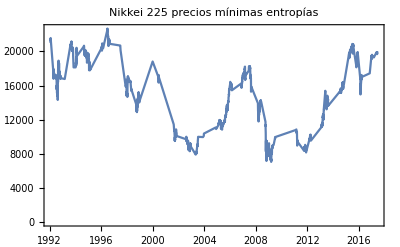
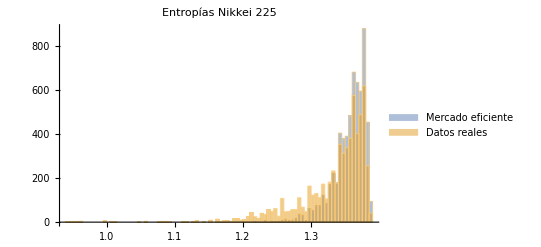
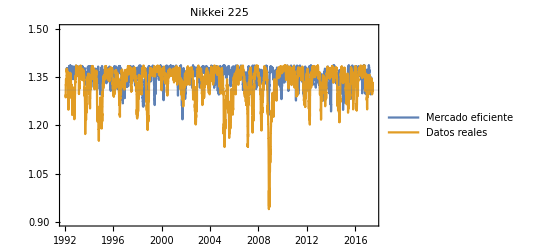
{12.454,23.1349 % de los precios no se comporta Gaussianamente -Graphics- -Graphics- -Graphics-}

```mathematica
AbsoluteTiming[ComparativeMarketEntropyThreshold[4,50]]
```

## Distribuciones sin Moving Average

```mathematica
Distribuciones[market_,dias_] :=Block[{MercadoSimulado,MercadoEficienteConFechas,dataSimulada,dataReal,ℋ,a,b,c,d,e,f,g,h},
MercadoSimulado = RandomVariate[NormalDistribution[],Length[MarketEntropy[market,dias][[All,2]]]];

MercadoEficienteConFechas = Transpose[{MAVReturns[market,dias][[All,1]],MercadoSimulado}];

dataSimulada = Map[Entropy,Partition[DiscretizeByQuartiles[MercadoEficienteConFechas[[All,2]]],dias,1]];
dataReal = Map[Entropy,Partition[DiscretizeByQuartiles[database[[market]]["Returns"]],dias,1]];


ℋ=DistributionFitTest[dataSimulada,dataReal,"HypothesisTestData"];


a=ℋ["TestDataTable",{"CramerVonMises","KolmogorovSmirnov","Kuiper","PearsonChiSquare","WatsonUSquare"}];

b=ℋ["TestConclusion",{"CramerVonMises","KolmogorovSmirnov","Kuiper","PearsonChiSquare","WatsonUSquare"}]//TraditionalForm;
a b
];
```

```mathematica
AbsoluteTiming[Distribuciones[4,50]]
```

General::munfl: 2.53442×10^-137 6.42328×10^-274 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-104017.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-416067.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{14.5999, | Statistic | P-Value
Cramér-von Mises | 3859.38 | 4.51861×10^-14
Kolmogorov-Smirnov | 8675683/38544872 | 0.
Kuiper | 4.08498 | 0.
Pearson χ^2 | 1299.55 | 2.82085×10^-232
Watson U^2 | 17.9721 | 0. {The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Cramér-von Mises test.,The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Kolmogorov-Smirnov test.,The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Kuiper test.,The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Pearson χ^2 test.,The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Watson U^2 test.}}

## 2. Tras ser filtrados por un MAV

```mathematica
PlotMarketEntropyThresholdMAV[market_,dias_] :=Block[{MercadoSimuladoMAV,MercadoEficienteConFechasMAV,MercadoPreciosSimulados,MercadoConPrecioSimuladoYFechas,MercadoPorcentuales,MercadoConFechasYPreciosMAV,Particion,Techo,SimulatedEntropy,GraficaConThresholdMAV},
MercadoSimuladoMAV = RandomVariate[NormalDistribution[],Length[MAVReturns[market,dias][[All,2]]]];
MercadoEficienteConFechasMAV = Transpose[{MAVReturns[market,dias][[All,1]],MercadoSimuladoMAV}];
MercadoPreciosSimulados = Accumulate[MercadoEficienteConFechasMAV[[All,2]]]+Abs[Min[Accumulate[MercadoEficienteConFechasMAV[[All,2]]]]];
MercadoConPrecioSimuladoYFechas =  Transpose[{MAVReturns[market,dias][[All,1]],MercadoPreciosSimulados}];
MercadoPorcentuales = MapAt[YearPercentual,MercadoConPrecioSimuladoYFechas,{All,1}];
MercadoConFechasYPreciosMAV=MapAt[DateFromYearPercentual,MovingAverage[MercadoPorcentuales,dias],{All,1}];
Particion = Partition[Transpose[{MercadoConFechasYPreciosMAV[[All,1]],DiscretizeByQuartiles[MercadoConFechasYPreciosMAV[[All,2]]]}],dias,1];
Techo = N[Quantile[Map[N[Entropy[#[[All,2]]]]&,Particion],0.1]];

SimulatedEntropy = Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,Particion];
GraficaConThresholdMAV = DateListPlot[{SimulatedEntropy,MarketEntropyMAV[market,dias]},GridLines->{{},{Techo}},
Frame->True,PlotLabel->database[[market]]["Name"],PlotLegends->{"Mercado eficiente" ,"Datos reales"},PlotRange->{-0.2,1.5}]
];
```

```mathematica
Datee[date_,p_]:= List[DateObject[Take[DateList[date],3]],p];
BuscarPrecio[datedPrices_,date_]:= FirstCase[datedPrices,{date,p_}:>p];
DatedPriceMarket[market_] := Apply[Datee,database[[market]]["DatedPrices"],{1}];
```

```mathematica
MinEntropyMarketMAV[market_,dias_] :=Block[{MercadoSimuladoMAV,MercadoEficienteConFechasMAV,MercadoPreciosSimulados,MercadoConPrecioSimuladoYFechas,MercadoPorcentuales,MercadoConFechasYPreciosMAV,Particion,Techo,MiniEntropiFechasMAV,FechasEncontradas,FechasFiltradas},
MercadoSimuladoMAV = RandomVariate[NormalDistribution[],Length[MAVReturns[market,dias][[All,2]]]];
MercadoEficienteConFechasMAV = Transpose[{MAVReturns[market,dias][[All,1]],MercadoSimuladoMAV}];
MercadoPreciosSimulados = Accumulate[MercadoEficienteConFechasMAV[[All,2]]]+Abs[Min[Accumulate[MercadoEficienteConFechasMAV[[All,2]]]]];
MercadoConPrecioSimuladoYFechas =  Transpose[{MAVReturns[market,dias][[All,1]],MercadoPreciosSimulados}];
MercadoPorcentuales = MapAt[YearPercentual,MercadoConPrecioSimuladoYFechas,{All,1}];
MercadoConFechasYPreciosMAV=MapAt[DateFromYearPercentual,MovingAverage[MercadoPorcentuales,dias],{All,1}];
Particion = Partition[Transpose[{MercadoConFechasYPreciosMAV[[All,1]],DiscretizeByQuartiles[MercadoConFechasYPreciosMAV[[All,2]]]}],dias,1];
Techo = N[Quantile[Map[N[Entropy[#[[All,2]]]]&,Particion],0.1]];
MiniEntropiFechasMAV = Select[CalculateMarketEntropyMAV[market,dias],Last[#] ≤ Techo &];

FechasEncontradas = Map[{#,BuscarPrecio[DatedPriceMarket[market],#]}&,MiniEntropiFechasMAV[[All,1]]];
FechasFiltradas = DeleteCases[FechasEncontradas,{_,_Missing}];(*con su precio*)
FechasFiltradas
];
```

```mathematica
MinEntropyMarketReturnsMAV[market_,dias_] := Block[{MercadoSimuladoMAV,MercadoEficienteConFechasMAV,MercadoPreciosSimulados,MercadoConPrecioSimuladoYFechas,MercadoPorcentuales,MercadoConFechasYPreciosMAV,Particion,Techo,MiniEntropiFechasMAV,FechasEncontradas,FechasFiltradas},
MercadoSimuladoMAV = RandomVariate[NormalDistribution[],Length[MAVReturns[market,dias][[All,2]]]];
MercadoEficienteConFechasMAV = Transpose[{MAVReturns[market,dias][[All,1]],MercadoSimuladoMAV}];
MercadoPreciosSimulados = Accumulate[MercadoEficienteConFechasMAV[[All,2]]]+Abs[Min[Accumulate[MercadoEficienteConFechasMAV[[All,2]]]]];
MercadoConPrecioSimuladoYFechas =  Transpose[{MAVReturns[market,dias][[All,1]],MercadoPreciosSimulados}];
MercadoPorcentuales = MapAt[YearPercentual,MercadoConPrecioSimuladoYFechas,{All,1}];
MercadoConFechasYPreciosMAV=MapAt[DateFromYearPercentual,MovingAverage[MercadoPorcentuales,dias],{All,1}];
Particion = Partition[Transpose[{MercadoConFechasYPreciosMAV[[All,1]],DiscretizeByQuartiles[MercadoConFechasYPreciosMAV[[All,2]]]}],dias,1];
Techo = N[Quantile[Map[N[Entropy[#[[All,2]]]]&,Particion],0.1]];
MiniEntropiFechasMAV = Select[MarketEntropyMAV[market,dias],Last[#] ≤ Techo &];

FechasEncontradas = Map[{#,BuscarPrecio[DatedPriceMarket[market],#]}&,MiniEntropiFechasMAV[[All,1]]];
FechasFiltradas = DeleteCases[FechasEncontradas,{_,_Missing}];(*con su precio*)


Transpose[{Drop[FechasFiltradas[[All,1]],-1],FechasFiltradas[[All,2]]//Returns}]
];
```

### Ahora todo junto CON MAV

```mathematica
ComparativeMarketEntropyThresholdMAV[market_,dias_] :=Block[{MercadoSimuladoMAV,MercadoEficienteConFechasMAV,MercadoPreciosSimulados,MercadoConPrecioSimuladoYFechas,MercadoPorcentuales,MercadoConFechasYPreciosMAV,Particion,Techo,SimulatedEntropy,GraficaConThresholdMAV,MiniEntropiFechasMAV,FechasEncontradas,FechasFiltradas,SinEntropiaConFechasReturns,PlotMinEntropyMarketMAV,CantidadSinEntropy,Histograma},
MercadoSimuladoMAV = RandomVariate[NormalDistribution[],Length[MAVReturns[market,dias][[All,2]]]];
MercadoEficienteConFechasMAV = Transpose[{MAVReturns[market,dias][[All,1]],MercadoSimuladoMAV}];
MercadoPreciosSimulados = Accumulate[MercadoEficienteConFechasMAV[[All,2]]]+Abs[Min[Accumulate[MercadoEficienteConFechasMAV[[All,2]]]]];
MercadoConPrecioSimuladoYFechas =  Transpose[{MAVReturns[market,dias][[All,1]],MercadoPreciosSimulados}];
MercadoPorcentuales = MapAt[YearPercentual,MercadoConPrecioSimuladoYFechas,{All,1}];
MercadoConFechasYPreciosMAV=MapAt[DateFromYearPercentual,MovingAverage[MercadoPorcentuales,dias],{All,1}];
Particion = Partition[Transpose[{MercadoConFechasYPreciosMAV[[All,1]],DiscretizeByQuartiles[MercadoConFechasYPreciosMAV[[All,2]]]}],dias,1];
Techo = N[Quantile[Map[N[Entropy[#[[All,2]]]]&,Particion],0.1]];
SimulatedEntropy = Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,Particion];
GraficaConThresholdMAV = DateListPlot[{SimulatedEntropy,MarketEntropyMAV[market,dias]},GridLines->{{},{Techo}},
Frame->True,PlotLabel->database[[market]]["Name"],PlotLegends->{"Mercado eficiente" ,"Datos reales"},PlotRange->{-0.2,1.55}];
MiniEntropiFechasMAV = Select[MarketEntropyMAV[market,dias],Last[#] ≤ Techo &];

FechasEncontradas = Map[{#,BuscarPrecio[DatedPriceMarket[market],#]}&,MiniEntropiFechasMAV[[All,1]]];
FechasFiltradas = DeleteCases[FechasEncontradas,{_,_Missing}];
SinEntropiaConFechasReturns = Transpose[{Drop[FechasFiltradas[[All,1]],-1],FechasFiltradas[[All,2]]//Returns}];
PlotMinEntropyMarketMAV = DateListPlot[FechasFiltradas,PlotLabel->database[[market]]["Name"] " precios mínimas entropías",PlotRange->All];
CantidadSinEntropy = N[Length[FechasFiltradas[[All,2]]]/Length[MarketEntropyMAV[market,dias][[All,2]]]];

Histograma = Histogram[{Map[Entropy,Partition[DiscretizeByQuartiles[MercadoConFechasYPreciosMAV[[All,2]]//Returns],dias,1]],Map[Entropy,Partition[DiscretizeByQuartiles[MAVReturns[market,dias][[All,2]]],dias,1]]},
PlotLabel->database[[market]]["Name"]"Entropías" ,BaseStyle->FontSize->16,ChartStyle->{ColorData[97][1],ColorData[97][2]},ChartLegends->{"Mercado eficiente","Datos reales"},PlotRange->Full];
GraficaConThresholdMAV PlotMinEntropyMarketMAV Histograma CantidadSinEntropy*100 "% tiene entropía mínima"

];
```

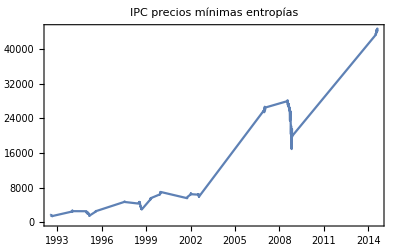
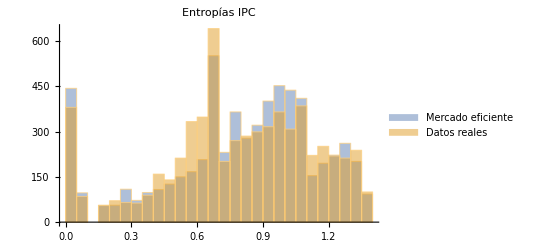
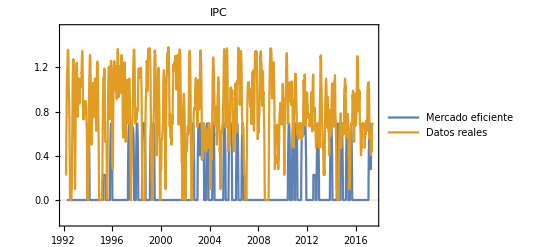
{81.1853,4.10395 % tiene entropía mínima -Graphics- -Graphics- -Graphics-}

```mathematica
AbsoluteTiming[ComparativeMarketEntropyThresholdMAV[3,50]]
```

## Distribuciones con Moving Average

```mathematica
DistribucionesMAV[market_,dias_] :=Block[{MercadoSimuladoMAV,MercadoEficienteConFechasMAV,MercadoPreciosSimulados,MercadoConPrecioSimuladoYFechas,MercadoPorcentuales,MercadoConFechasYPreciosMAV,dataSimuladaMAV,dataRealMAV,ℋ,a,b,c},
MercadoSimuladoMAV = RandomVariate[NormalDistribution[],Length[MAVReturns[market,dias][[All,2]]]];
MercadoEficienteConFechasMAV = Transpose[{MAVReturns[market,dias][[All,1]],MercadoSimuladoMAV}];
MercadoPreciosSimulados = Accumulate[MercadoEficienteConFechasMAV[[All,2]]]+Abs[Min[Accumulate[MercadoEficienteConFechasMAV[[All,2]]]]];
MercadoConPrecioSimuladoYFechas =  Transpose[{MAVReturns[market,dias][[All,1]],MercadoPreciosSimulados}];
MercadoPorcentuales = MapAt[YearPercentual,MercadoConPrecioSimuladoYFechas,{All,1}];
MercadoConFechasYPreciosMAV=MapAt[DateFromYearPercentual,MovingAverage[MercadoPorcentuales,dias],{All,1}];
dataSimuladaMAV = Map[Entropy,Partition[DiscretizeByQuartiles[MercadoConFechasYPreciosMAV[[All,2]]//Returns],dias,1]];
dataRealMAV = Map[Entropy,Partition[DiscretizeByQuartiles[MAVReturns[market,dias][[All,2]]],dias,1]];
KolmogorovSmirnovTest[dataSimuladaMAV,dataRealMAV];
ℋ=DistributionFitTest[dataSimuladaMAV,dataRealMAV,"HypothesisTestData"];

ℋ["Properties"];

a =ℋ["TestDataTable",All];
b = ℋ["TestConclusion",All]//TraditionalForm;
ℋ["TestDataTable","DistanceToBoundary"];
(*ℋ["FittedDistribution"]*)
a b
];
```

```mathematica
AbsoluteTiming[DistribucionesMAV[3,50]]
```

General::munfl: Exp[-100587.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-402347.] is too small to represent as a normalized machine number; precision may be lost.

DistributionFitTest::tstdm: There are 1 datasets present, but the tests in DistanceToBoundary require 2 datasets.

DistributionFitTest::ntunf: The DistanceToBoundary test cannot be used to assess fit to {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«6261»}. The DistanceToBoundary test is only useful as a test for uniformity.

{33.0074, | Statistic | P-Value
Anderson-Darling | 0.512784 | 0.733798
Cramér-von Mises | 3263.63 | 4.44089×10^-14
Kolmogorov-Smirnov | 771660/13171057 | 8.52187×10^-10
Kuiper | 3.99227 | 0.
Pearson χ^2 | 326.874 | 1.21449×10^-37
Watson U^2 | 0.697041 | 1.50036×10^-6 {The null hypothesis that the datasets have the same distribution is not rejected at the 5 percent level based on the Anderson-Darling test.,The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Cramér-von Mises test.,The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Kolmogorov-Smirnov test.,The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Kuiper test.,The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Pearson χ^2 test.,The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Watson U^2 test.}}